```mathematica
data=Import["puzzle.csv"];
```

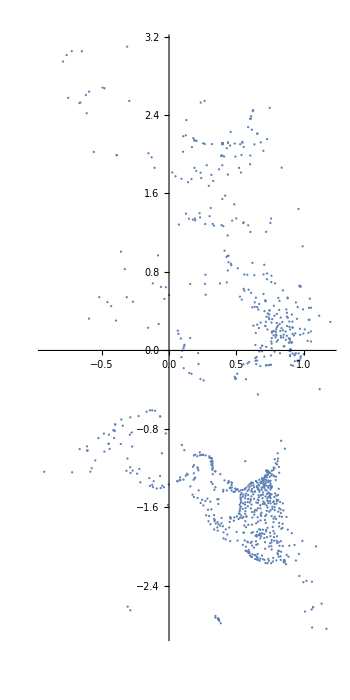

```mathematica
ListPlot[data, AspectRatio->2]
```

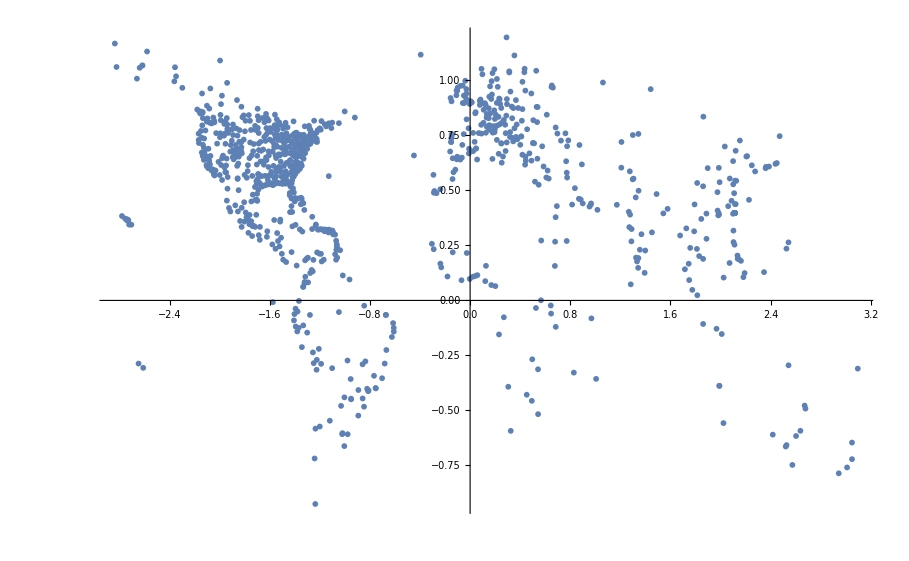

```mathematica
ListPlot[Reverse/@data]
```

```mathematica
Show[Graphics[{Red,Disk[{2.1136286,0.3971497},0.05]}],GeoGraphics[GeoRange->"World"],ListPlot[Reverse@*({57.28444637300546,57.29568167110497}*#&)/@(data),AspectRatio->1/3]]
```

-Graphics-

```mathematica
SortBy[Tally[data],-#[[2]]&][[1;;10]]
```

{{{0.39715,2.11363},101},{{-0.388084,1.99123},2},{{-0.0659085,-0.672521},2},{{0.0618409,-1.33311},2},{{0.636612,-1.43828},2},{{0.690307,0.0478013},2},{{0.713595,0.249422},2},{{0.715182,0.50291},2},{{0.719915,-0.151519},2},{{0.745198,0.408607},2}}

```mathematica
(*
Each coordinate is an earth location, caled by about 57.3, and flipped diagonally. The coordinates appear to correspond to airports. For example, the only repeated coordinate is {2.1136286,0.3971497}, corresponding to the world coordinate {22.75667781,121.11091878}, which points to the Taitung airport in Taiwan, but I don't know its significance.
*)
```